# Title

Author Name

Abstract

## Section

XXXX:

## Mathematical Induction

```mathematica
WikipediaSearch["Mathematical Induction"]
```

{Mathematical induction}

We started discussing the process for proof by induction.

We started the Principal of Mathematical Induction. We used this to describe process for writing an induction proof.

Our statement will have a universal quantifier and a predicate statement.

∀n∈ℕ(P(n))

For a particular n value, you obtain a mathematical (logical) statement.

Proof by PMI:

Prove: (∀n∈ℕ)(P(n))

Step 1:

Verify P(1) is true.

Step 2:

If P(k) is true, then P(k+1) is true.

Then P(n) holds for all n∈ℕ.

Proposition: For all n∈ℕ

1^2+2^2+…+n^2=1/6*n(n+1)(2n+1)

∑_(j=1)^n j^2=(n(n+1)(2n+1))/b:P(n)

Proof:

We will prove using PMI.

First we must verify that P(1) is true.

For n=1, we have ∑_(j=1)^1 j^2=1^2=1 (LHS)

For n=1 we have (1(1+1)(2*1+1))/6 RHS.

```mathematica
(n↦(n(n+1)(2n+1))/6)[1]
```

1

```mathematica
∑_(j=1)^n j^k
```

HarmonicNumber[n,-k]

```mathematica
∑_(j=1)^n j^k//TraditionalForm
```

n-k

```mathematica
HarmonicNumber[Range[9],-3]
```

{1,9,36,100,225,441,784,1296,2025}

```mathematica
Table[∑_(j=1)^n j^3,{n,9}]
```

{1,9,36,100,225,441,784,1296,2025}

```mathematica
RSolve[{t[0]==0,t[n]==2t[n-1]+1},t[n],n]
```

{{t[n]→-1+2^n}}

```mathematica
t[n_]:=-1+2^n
```

```mathematica
Table[t[k],{k,10}]
```

{1,3,7,15,31,63,127,255,511,1023}

```mathematica
t[64]
```

18446744073709551615

```mathematica
Quantity[t[64],"Seconds"]
```

18446744073709551615 s

```mathematica
HarmonicNumber[4,r]
```

1+2^-r+3^-r+4^-r

```mathematica
HarmonicNumber[4,r]//TraditionalForm
```

2^-r+3^-r+4^-r+1

```mathematica
HarmonicNumber[z,4]//TraditionalForm
```

z4

```mathematica
HarmonicNumber[z,-4]//TraditionalForm
```

z^5/5+z^4/2+z^3/3-z/30

```mathematica
HarmonicNumber[∞,2]//TraditionalForm
```

π^2/6

```mathematica
HarmonicNumber[∞,4]//TraditionalForm
```

π^4/90

```mathematica
HarmonicNumber[∞,2Range[10]]//TraditionalForm
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555,(691 π^12)/638512875,(2 π^14)/18243225,(3617 π^16)/325641566250,(43867 π^18)/38979295480125,(174611 π^20)/1531329465290625}

```mathematica
FunctionDomain[HarmonicNumber[x],x]
```

x≥0||x∉ℤ

```mathematica
FunctionDomain[HarmonicNumber[x],x,Complexes]
```

Re[x]≥0||x∉ℤ

```mathematica
FunctionDomain[HarmonicNumber[x],x,Complexes]
```

Re[x]≥0||x∉ℤ

```mathematica
FunctionRange[HarmonicNumber[x],x,y]
```

True

```mathematica
FunctionMeromorphic[HarmonicNumber[x],x]
```

True

```mathematica
FunctionMonotonicity[HarmonicNumber[x],x]
```

Indeterminate

```mathematica
FunctionInjective[HarmonicNumber[x],x]
```

False

Now we need to show for k∈ℕ, P(k) true implies P(k+1) is true. We will take the direct approach.

```mathematica
FunctionSurjective[HarmonicNumber[x],x]
```

True

```mathematica
FunctionSign[HarmonicNumber[x],x]
```

Indeterminate

```mathematica
FunctionSingularities[HarmonicNumber[x],x]
```

Sin[π x]==0&&x≤-1

```mathematica
FunctionDiscontinuities[HarmonicNumber[x],x]
```

Sin[π x]==0&&x≤-1

```mathematica
FunctionConvexity[HarmonicNumber[x],x]
```

Indeterminate

```mathematica
HarmonicNumber[n,k]//TraditionalForm
```

nk

```mathematica
D[HarmonicNumber[n],n]
```

π^2/6-HarmonicNumber[n,2]

```mathematica
Table[D[HarmonicNumber[n],{n,k}],{k,1,5}]//FullSimplify
```

{PolyGamma[1,1+n],PolyGamma[2,1+n],PolyGamma[3,1+n],PolyGamma[4,1+n],PolyGamma[5,1+n]}

```mathematica
Table[D[HarmonicNumber[n],{n,k}],{k,1,5}]//FullSimplify//TraditionalForm
```

{1n+1,2n+1,3n+1,4n+1,5n+1}

```mathematica
D[HarmonicNumber[n],{n,k}]//FullSimplify
```

Piecewise[{{(-1)^k n^(-1-k) k!+PolyGamma[k,n], k≥1}, {HarmonicNumber[n], True}}]

Suppose P(x) is true.

That is ∑_(j=1)^k j^2=1/6(k+1)(2k+1).

```mathematica
Apart[1/6(k+1)(2k+1)]
```

1/6+k/2+k^2/3

```mathematica
Together[Apart[1/6(k+1)(2k+1)]]
```

1/6 (1+3 k+2 k^2)

```mathematica
∑_(k=1)^∞ 1/6 (1+3 k+2 k^2)
```

∑_(k=1)^∞ 1/6 (1+3 k+2 k^2)

We want to s how that this equation we can obtain

```mathematica
GeoGraphics`$GeoBackgroundType="Vector"
```

Vector

```mathematica
Series[HarmonicNumber[n],{n,0,5}]//TraditionalForm
```

(π^2 n)/6+(n^2 21)/2+(π^4 n^3)/90+(n^4 41)/24+(π^6 n^5)/945+O(n^6)

```mathematica
GeoGraphics[Here]
```

-Graphics-

```mathematica
GeoGraphics[Here,ImageSize->Full]
```

-Graphics-

Let's practice writing induction proofs.

```mathematica
Sum[j^2,{j,n}]
```

1/6 n (1+n) (1+2 n)

prove by induction ∑_(j=1)^n j^2 is 1/6(n)(1+n)(1+2n)

WolframAlphaQueryResults

```mathematica
∑_(i=1)^n 1/(i(i+1))
```

1-1/(1+n)

```mathematica
Together[∑_(i=1)^n 1/(i(i+1))]
```

n/(1+n)

```mathematica
∑_(i=1)^n (2i-1)
```

n^2

```mathematica
∑_(j=1)^n j
```

1/2 n (1+n)

```mathematica
3+∑_(i=1)^n (3+5i)
```

3+1/2 (11 n+5 n^2)

```mathematica
Simplify[3+1/2 (11 n+5 n^2)]
```

1/2 (6+11 n+5 n^2)

```mathematica
Factor[Simplify[3+1/2 (11 n+5 n^2)]]
```

1/2 (1+n) (6+5 n)

```mathematica
∑_(i=1)^n i^4
```

1/30 n (1+n) (1+2 n) (-1+3 n+3 n^2)

```mathematica
FullSimplify[1/30 n (1+n) (1+2 n) (-1+3 n+3 n^2)]
```

1/30 n (1+n) (1+2 n) (-1+3 n (1+n))

```mathematica
Expand[FullSimplify[1/30 n (1+n) (1+2 n) (-1+3 n+3 n^2)]]
```

-n/30+n^3/3+n^4/2+n^5/5

```mathematica
3+∑_(i=1)^n (3+5i)
```

3+1/2 (11 n+5 n^2)

```mathematica
Simplify[3+∑_(i=1)^n (3+5i)]
```

1/2 (6+11 n+5 n^2)

```mathematica
(n↦(n+1)(5n+6))[k+1]
```

(2+k) (6+5 (1+k))

```mathematica
Expand[(n↦(n+1)(5n+6))[k+1]]
```

22+21 k+5 k^2

```mathematica
∑_(i=1)^(k+1) (3+5i)
```

1/2 (16+21 k+5 k^2)

```mathematica
Simplify[1/2 (16+21 k+5 k^2)]
```

8+(21 k)/2+(5 k^2)/2

```mathematica
Factor[(5 k^2+21k+16)]
```

(1+k) (16+5 k)

```mathematica
10k+10+(k+1)(5k+6)
```

10+10 k+(1+k) (6+5 k)

```mathematica
Expand[10k+10+(k+1)(5k+6)]
```

16+21 k+5 k^2

```mathematica
Factor[Expand[10k+10+(k+1)(5k+6)]]
```

(1+k) (16+5 k)

```mathematica
10k+
```

```mathematica
Factor[5 k^2+21k+22]
```

(2+k) (11+5 k)

```mathematica
(((k+1)+1)(5(k+1)+6))/2
```

1/2 (2+k) (6+5 (1+k))

```mathematica
(((k+1)+1)(5(k+1)+6))/2==((2+k)(11+5k))/2//FullSimplify
```

True

```mathematica
∑_(k=1)^n 2k-1
```

-1+n (1+n)

```mathematica
Simplify[-1+n (1+n)]
```

-1+n+n^2

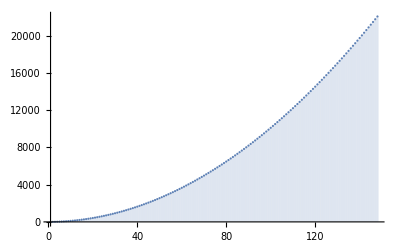

```mathematica
DiscretePlot[Simplify[-1+n (1+n)],{n,Round[E^5]}]
```

```mathematica
∑_(k=1)^n ∑_(l=1)^k (2l-1)
```

1/6 n (1+n) (1+2 n)

```mathematica
∑_(k=1)^n -1+k+k^2
```

k+k^2-n

```mathematica
∑_(l=1)^k (2l-1)
```

k^2

```mathematica
∑_(k=1)^n 4^k
```

4/3 (-1+4^n)

```mathematica
∑_(k=1)^n 4^k//TraditionalForm
```

4/3 (4^n-1)

```mathematica
∑_(k=1)^n 4^k//Expand//TraditionalForm
```

4^(n+1)/3-4/3

```mathematica
∑_(k=1)^n 4^k//Expand//PowerExpand//TraditionalForm
```

4^(n+1)/3-4/3

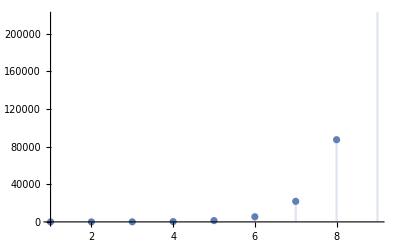

```mathematica
DiscretePlot[∑_(k=1)^n 4^k//Expand//PowerExpand,{n,9}]
```

```mathematica
∑_(i=1)^n 1/(i+1)
```

-1+EulerGamma+PolyGamma[0,2+n]

```mathematica
∑_(i=1)^n 1/(i+1)//TraditionalForm
```

0n+2+ℽ-1

```mathematica
FunctionDomain[PolyGamma[0,n],n]
```

n≥1||n∉ℤ

```mathematica
PolyGamma[x,2]
```

PolyGamma[x,2]

```mathematica
ComplexPlot3D[PolyGamma[x,2],{x,-2-2I,2+2I}]
```

-Graphics3D-

```mathematica
∫PolyGamma[x,2]ⅆx
```

∫PolyGamma[x,2]ⅆx

```mathematica
Asymptotic[∑_(i=1)^n 1/(i+1),n->∞]
```

Log[n]

```mathematica
Asymptotic[∑_(i=1)^n 1/(i+1),n->∞,SeriesTermGoal->3]//TraditionalForm
```

1/n^3-13/(12 n^2)+3/(2 n)+log(n)+ℽ-1

```mathematica
DiscreteAsymptotic[∑_(i=1)^n 1/(i+1),n->∞,SeriesTermGoal->3]//TraditionalForm
```

1/n^3-13/(12 n^2)+3/(2 n)+log(n)+ℽ-1

```mathematica
AsymptoticSum[Log[k],{k,1,n},n->∞]//TraditionalForm
```

log((√(2 π) √n+(√(π/2))/(6 √n)) ⅇ^(n (log(n)-1)))

```mathematica
∑_(k=1)^n Log[k]
```

Log[Pochhammer[1,n]]

```mathematica
Series[AsymptoticSum[Log[k],{k,1,n},n->∞]-∑_(k=1)^n Log[k],{n,1,7}]//TraditionalForm
```

1/2 (-2-3 log(2)-2 log(3)+2 log(13)+log(π))+(ℽ-15/26) (n-1)+((1671-169 π^2) (n-1)^2)/2028+(n-1)^3 (-469/6591-22/6)+(n-1)^4 (18389/685464+1/4 (-((1-ℽ+ℽ^2/2-π^2/12) (-1+(1-ℽ)^2+π^2/6))-(1-ℽ) (-2/3+ℽ-ℽ^2/2+ℽ^3/6+π^2/12-(ℽ π^2)/12-22/6)-1/2 (ℽ-1) ((1-ℽ)^3+3 (1-ℽ) (π^2/6-1)+22)+1/6 (-(1-ℽ)^4-6 (1-ℽ)^2 (π^2/6-1)-3 (π^2/6-1)^2-6 (π^4/90-1)-4 (1-ℽ) 22)))+(n-1)^5 (1/5 (-((-1+(1-ℽ)^2+π^2/6) (-2/3+ℽ-ℽ^2/2+ℽ^3/6+π^2/12-(ℽ π^2)/12-22/6))-1/2 (1-ℽ+ℽ^2/2-π^2/12) ((1-ℽ)^3+3 (1-ℽ) (π^2/6-1)+22)-1/6 (ℽ-1) ((1-ℽ)^4+6 (1-ℽ)^2 (π^2/6-1)+3 (π^2/6-1)^2+6 (π^4/90-1)+4 (1-ℽ) 22)-(1-ℽ) (2/3-(2 ℽ)/3+ℽ^2/2-ℽ^3/6+ℽ^4/24-π^2/12+(ℽ π^2)/12-(ℽ^2 π^2)/24+π^4/1440+22/6-(ℽ 22)/6)+1/24 (-(1-ℽ)^5-10 (1-ℽ)^3 (π^2/6-1)-15 (1-ℽ) (π^2/6-1)^2-30 (1-ℽ) (π^4/90-1)-10 (1-ℽ)^2 22-10 (π^2/6-1) 22-42))-118551/7425860)+(n-1)^6 (3927823/289608540+1/6 (-1/2 (-2/3+ℽ-ℽ^2/2+ℽ^3/6+π^2/12-(ℽ π^2)/12-22/6) ((1-ℽ)^3+3 (1-ℽ) (π^2/6-1)+22)-1/6 (1-ℽ+ℽ^2/2-π^2/12) ((1-ℽ)^4+6 (1-ℽ)^2 (π^2/6-1)+3 (π^2/6-1)^2+6 (π^4/90-1)+4 (1-ℽ) 22)-(-1+(1-ℽ)^2+π^2/6) (2/3-(2 ℽ)/3+ℽ^2/2-ℽ^3/6+ℽ^4/24-π^2/12+(ℽ π^2)/12-(ℽ^2 π^2)/24+π^4/1440+22/6-(ℽ 22)/6)-(1-ℽ) (-7/15+(2 ℽ)/3-ℽ^2/3+ℽ^3/6-ℽ^4/24+ℽ^5/120+π^2/18-(ℽ π^2)/12+(ℽ^2 π^2)/24-(ℽ^3 π^2)/72-π^4/1440+(ℽ π^4)/1440-22/6+(ℽ 22)/6-(ℽ^2 22)/12+(π^2 22)/72-42/120)-1/24 (ℽ-1) ((1-ℽ)^5+10 (1-ℽ)^3 (π^2/6-1)+15 (1-ℽ) (π^2/6-1)^2+30 (1-ℽ) (π^4/90-1)+10 (1-ℽ)^2 22+10 (π^2/6-1) 22+42)+1/120 (-(1-ℽ)^6-15 (1-ℽ)^4 (π^2/6-1)-45 (1-ℽ)^2 (π^2/6-1)^2-15 (π^2/6-1)^3-90 (1-ℽ)^2 (π^4/90-1)-90 (π^2/6-1) (π^4/90-1)-120 (π^6/945-1)-20 (1-ℽ)^3 22-60 (1-ℽ) (π^2/6-1) 22-10 22^2-6 (1-ℽ) 42)))+(-18001610/1317718857+1/7 (-1/6 (-2/3+ℽ-ℽ^2/2+ℽ^3/6+π^2/12-(ℽ π^2)/12-22/6) ((1-ℽ)^4+6 (1-ℽ)^2 (-1+π^2/6)+3 (-1+π^2/6)^2+6 (-1+π^4/90)+4 (1-ℽ) 22)-1/2 ((1-ℽ)^3+3 (1-ℽ) (-1+π^2/6)+22) (2/3-(2 ℽ)/3+ℽ^2/2-ℽ^3/6+ℽ^4/24-π^2/12+(ℽ π^2)/12-(ℽ^2 π^2)/24+π^4/1440+22/6-(ℽ 22)/6)-(-1+(1-ℽ)^2+π^2/6) (-7/15+(2 ℽ)/3-ℽ^2/3+ℽ^3/6-ℽ^4/24+ℽ^5/120+π^2/18-(ℽ π^2)/12+(ℽ^2 π^2)/24-(ℽ^3 π^2)/72-π^4/1440+(ℽ π^4)/1440-22/6+(ℽ 22)/6-(ℽ^2 22)/12+(π^2 22)/72-42/120)-1/24 (1-ℽ+ℽ^2/2-π^2/12) ((1-ℽ)^5+10 (1-ℽ)^3 (-1+π^2/6)+15 (1-ℽ) (-1+π^2/6)^2+30 (1-ℽ) (-1+π^4/90)+10 (1-ℽ)^2 22+10 (-1+π^2/6) 22+42)-1/120 (-1+ℽ) ((1-ℽ)^6+15 (1-ℽ)^4 (-1+π^2/6)+45 (1-ℽ)^2 (-1+π^2/6)^2+15 (-1+π^2/6)^3+90 (1-ℽ)^2 (-1+π^4/90)+90 (-1+π^2/6) (-1+π^4/90)+120 (-1+π^6/945)+20 (1-ℽ)^3 22+60 (1-ℽ) (-1+π^2/6) 22+10 22^2+6 (1-ℽ) 42)-(1-ℽ) (47/90-(7 ℽ)/15+ℽ^2/3-ℽ^3/9+ℽ^4/24-ℽ^5/120+ℽ^6/720-π^2/18+(ℽ π^2)/18-(ℽ^2 π^2)/24+(ℽ^3 π^2)/72-(ℽ^4 π^2)/288+π^4/1440-(ℽ π^4)/1440+(ℽ^2 π^4)/2880-π^6/24192+22/9-(ℽ 22)/6+(ℽ^2 22)/12-(ℽ^3 22)/36-(π^2 22)/72+1/72 ℽ π^2 22+22^2/72+42/120-(ℽ 42)/120)+1/720 (-(1-ℽ)^7-21 (1-ℽ)^5 (-1+π^2/6)-105 (1-ℽ)^3 (-1+π^2/6)^2-105 (1-ℽ) (-1+π^2/6)^3-210 (1-ℽ)^3 (-1+π^4/90)-630 (1-ℽ) (-1+π^2/6) (-1+π^4/90)-840 (1-ℽ) (-1+π^6/945)-35 (1-ℽ)^4 22-210 (1-ℽ)^2 (-1+π^2/6) 22-105 (-1+π^2/6)^2 22-210 (-1+π^4/90) 22-70 (1-ℽ) 22^2-21 (1-ℽ)^2 42-21 (-1+π^2/6) 42-62))) (n-1)^7+O((n-1)^8)

```mathematica
Cube[]
```

Cube[]

```mathematica
CanonicalizePolyhedron[Cube[]]
```

Polyhedron[…]

```mathematica
EulerCharacteristic[CanonicalizePolyhedron[Cube[]]]
```

2

```mathematica
CanonicalizePolyhedron[Dodecahedron[]]
```

Polyhedron[…]

```mathematica
EulerCharacteristic[Dodecahedron[]]
```

2

```mathematica
EulerCharacteristic[CanonicalizePolyhedron[Dodecahedron[]]]
```

2

```mathematica
∑_(k=1)^n k
```

1/2 n (1+n)

```mathematica
∑_(k=1)^n k//TraditionalForm
```

1/2 n (n+1)

```mathematica
CanonicalizePolyhedron[Torus[]]
```

CanonicalizePolyhedron[Torus[]]

```mathematica
DiscretizeRegion[Torus[]]
```

-Graphics3D-

```mathematica
EulerCharacteristic[DiscretizeRegion[Torus[]]]
```

0

```mathematica
CanonicalizePolygon[Rectangle[]]
```

Polygon[…]

```mathematica
EulerCharacteristic[CanonicalizePolygon[Rectangle[]]]
```

0

```mathematica
Icosahedron[]
```

Icosahedron[]

```mathematica
CanonicalizePolyhedron[Icosahedron[]]
```

Polyhedron[…]

```mathematica
EulerCharacteristic[CanonicalizePolyhedron[Icosahedron[]]]
```

2

```mathematica
CanonicalizePolyhedron[Tetrahedron[]]
```

Polyhedron[…]

```mathematica
CanonicalizePolyhedron[Cuboid[3]]
```

CanonicalizePolyhedron[Cuboid[3]]

```mathematica
Cuboid[3]
```

Cuboid[3]

```mathematica
CanonicalizeRegion[Cuboid[3]]
```

CanonicalizeRegion[Cuboid[3]]

```mathematica
CanonicalizePolyhedron[Hexahedron[{3}]]
```

CanonicalizePolyhedron[Hexahedron[{3}]]

```mathematica
RandomReal[{4},{8,2}]
```

{{3.89822,2.54437},{1.92383,0.0725192},{2.82396,3.53559},{3.0887,0.343286},{2.78223,3.19034},{2.58099,3.67779},{3.56988,2.74215},{0.0590283,2.18869}}

```mathematica
Hexahedron[RandomReal[{4},{8,2}]]
```

Hexahedron[{{2.90697,3.25977},{0.81167,0.457123},{0.115886,2.73557},{2.76105,3.58104},{1.42776,0.0913215},{2.35744,3.59528},{3.97431,2.04701},{2.30088,2.5679}}]

```mathematica
CanonicalizePolyhedron[Hexahedron[RandomReal[{4},{8,2}]]]
```

CanonicalizePolyhedron[Hexahedron[{{2.27177,1.3866},{3.10248,3.53457},{2.04218,1.73545},{0.632451,3.56699},{2.35506,3.73564},{3.87066,3.82712},{2.90687,3.57703},{2.09153,0.317076}}]]

```mathematica
RegionQ[Hexahedron[RandomReal[{4},{8,3}]]]
```

True

```mathematica
MeshRegionQ[Hexahedron[RandomReal[{4},{8,3}]]]
```

False

```mathematica
Hexahedron[RandomReal[{4},{8,3}]]
```

Hexahedron[{{0.482188,1.42526,2.1948},{3.30857,2.89504,2.73657},{0.18676,1.23052,0.877625},{1.38156,2.76181,0.427932},{0.795076,0.262326,3.01034},{0.325288,0.0295712,0.379917},{1.46624,0.631584,2.13956},{1.3345,2.74131,3.86022}}]

```mathematica
DiscretizeRegion[Hexahedron[RandomReal[{4},{8,3}]]]
```

DiscretizeRegion[Hexahedron[{{2.52913,3.8701,3.92277},{3.94915,3.62987,1.69332},{2.32454,1.46429,2.5193},{2.55327,0.561739,2.47909},{0.197693,2.21426,2.89341},{2.66219,0.292052,1.87852},{0.0974086,1.01037,3.94402},{3.74557,1.55074,3.41849}}]]

```mathematica
PolyhedronDecomposition[Icosahedron[]]
```

{Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…]}

```mathematica
PolyhedronDecomposition[Dodecahedron[]]
```

{Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…]}

```mathematica
UniformPolyhedron["Icosidodecahedron"]
```

Polyhedron[…]

```mathematica
PolyhedronDecomposition[UniformPolyhedron["Icosidodecahedron"]]
```

{Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…],Polyhedron[…]}

```mathematica
SimplePolyhedronQ[Dodecahedron[]]
```

True

```mathematica
DualPolyhedron[Dodecahedron[]]
```

Icosahedron[1/10 (5+3 √5)]

```mathematica
CanonicalizePolyhedron[DualPolyhedron[Dodecahedron[]]]
```

Polyhedron[…]